```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/DESI/math

### w/o DM

```mathematica
DESY2s=Import["DESY2s.csv"];
```

```mathematica
DESY2sMean=Mean[DESY2s]
```

{-0.723974,-1.06981}

```mathematica
DESY2spol=Sort[Table[{Norm[DESY2s[[i]]-DESY2sMean],ArcTan[(DESY2s[[i]]-DESY2sMean)[[1]],(DESY2s[[i]]-DESY2sMean)[[2]]]},{i,Length[DESY2s]}],#1[[2]]<#2[[2]]&];
```

```mathematica
DESY2ssorted=Table[{DESY2spol[[i,1]]Cos[DESY2spol[[i,2]]],DESY2spol[[i,1]]Sin[DESY2spol[[i,2]]]}+DESY2sMean,{i,Length[DESY2spol]}];
```

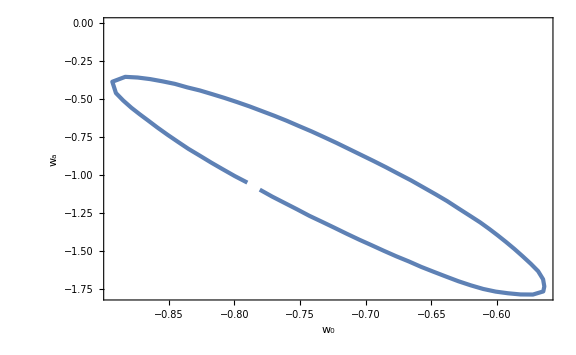

```mathematica
ListPlot[DESY2ssorted,FrameLabel->{Subscript[w, 0],Subscript[w, a]}]
```

```mathematica
e1[w0_]=3/2(1+w0);
e2[w0_,wa_]=-wa/(1+w0);
beta[w0_,wa_]=-e1[w0]+1/2 e2[w0,wa];
```

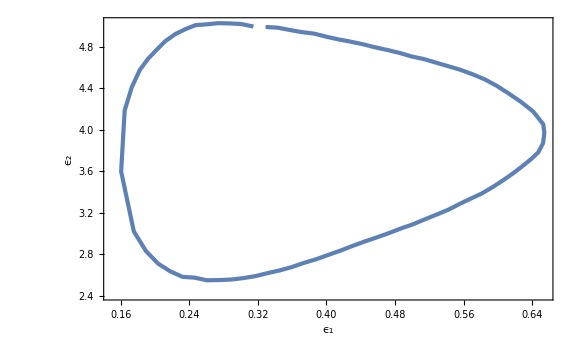

```mathematica
ListPlot[Map[{e1[#[[1]]],e2[#[[1]],#[[2]]]}&,DESY2ssorted],FrameLabel->{Subscript[ϵ, 1],Subscript[ϵ, 2]}]
```

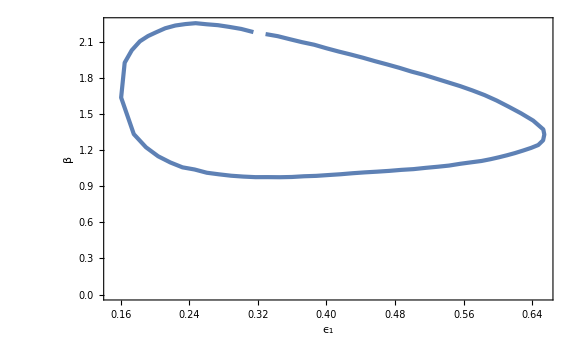

```mathematica
ListPlot[Map[{e1[#[[1]]],beta[#[[1]],#[[2]]]}&,DESY2ssorted],FrameLabel->{Subscript[ϵ, 1],β}]
```

```mathematica
H[x_]=A Cos[Sqrt[β/2]x];
```

```mathematica
V[x_]=3 H[x]^2-2 H'[x]^2//FullSimplify
```

1/2 A^2 (3-β+(3+β) Cos[√2 x √β])

```mathematica
eH[x_]=2(H'[x]/H[x])^2//FullSimplify
```

β Tan[(x √β)/(√2)]^2

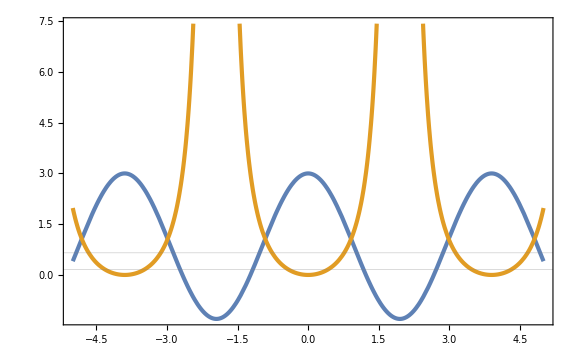

```mathematica
Plot[{V[x]/.{β->1.3,A->1},eH[x]/.{β->1.3}},{x,-5,5},GridLines->{None,{Min[e1[DESY2ssorted[[All,1]]]],Max[e1[DESY2ssorted[[All,1]]]]}}]
```

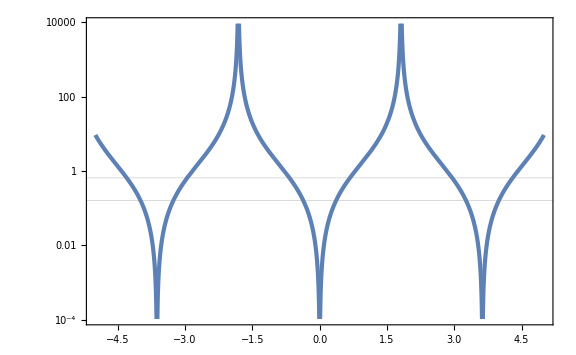

```mathematica
LogPlot[eH[x]/.{β->1.5,A->1},{x,-5,5},GridLines->{None,{Min[e1[DESY2ssorted[[All,1]]]],Max[e1[DESY2ssorted[[All,1]]]]}}]
```

```mathematica
x0=x/.Solve[eH[x]==e10,x][[2]]/.{C[1]->0}
```

(√2 ArcTan[(√e10)/(√β)])/(√β)

```mathematica
p0=Sqrt[2e10];
```

```mathematica
As=A/.Solve[p0^2/2+V[x0]/H0^2==3(1-Ωm),A][[2]]
```

(√2 H0 √(3-e10-3 Ωm))/(√(3-β+(3+β) Cos[2 ArcTan[(√e10)/(√β)]]))

```mathematica
Ωs[x_,p_]=1/3(p^2/2+V[x]/H0^2)/.{A->As}
Htot[z_,x_,p_]=Sqrt[Ωm (1+z)^3(*+Ωr H0^2(1+z)^4*)+Ωs[x,p]]//Simplify
```

1/3 (p^2/2+((3-e10-3 Ωm) (3-β+(3+β) Cos[√2 x √β]))/(3-β+(3+β) Cos[2 ArcTan[(√e10)/(√β)]]))

(√(p^2+6 (1+z)^3 Ωm-(2 (-3+e10+3 Ωm) (3-β+(3+β) Cos[√2 x √β]))/(3-β+(3+β) Cos[2 ArcTan[(√e10)/(√β)]])))/(√6)

```mathematica
Htot[0,x0,p0]//Simplify
```

1

```mathematica
pc=3086/1000 10^16(*m*);
H0s=(68 10^3)/(10^6 pc);
H0s//N
```

2.2035×10^-18

```mathematica
t0=H0s 138 10^8 60 60 24 36525/100;
t0//N
```

0.959613

```mathematica
ti=10^-4;
xi=28/100;
EoM=Simplify[{x''[t]+3Htot[z[t],x[t],x'[t]]x'[t]+V'[x[t]]/H0^2==0/.{A->As}(*,x[t0]==x0*),x[ti]==xi,x'[ti]==0(*8907/10000 p0*),
z'[t]==-Htot[z[t],x[t],x'[t]](1+z[t]),z[t0]==0}/.{β->15/10,e10->4/10,Ωm->3/10}]
```

{969 √3 Sin[√3 x[t]]==2 √390 x'[t] √(791+969 Cos[√3 x[t]]+1404 z[t]+1404 z[t]^2+468 z[t]^3+260 x'[t]^2)+520 x''[t],25 x[1/10000]==7,x'[1/10000]==0,z'[t]==-((1+z[t]) √(791+969 Cos[√3 x[t]]+1404 z[t]+1404 z[t]^2+468 z[t]^3+260 x'[t]^2))/(2 √390),z[46271331/48218750]==0}

```mathematica
sol=NDSolve[EoM,{x[t],x'[t],z[t]},{t,ti,t0}(*,WorkingPrecision->30*)][[1]]
```

{x[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t]}

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
zsol[t_]=z[t]/.sol;
Hsol[t_]=Htot[zsol[t],xsol[t],psol[t]]/.{β->15/10,e10->4/10,Ωm->3/10};
esol[t_]=psol[t]^2/(2 Hsol[t]^2);
Ωssol[t_]=Ωs[xsol[t],psol[t]]/.{β->15/10,e10->4/10,Ωm->3/10};
wsol[t_]=(1/3(psol[t]^2/2-V[xsol[t]]/H0^2/.{A->As}))/Ωssol[t]/.{β->15/10,e10->4/10,Ωm->3/10};
wasol[t_]=(1+zsol[t])^2/zsol'[t] wsol'[t];
```

```mathematica
{wsol[t0],wasol[t0]}
```

{-0.809321,-0.671206}

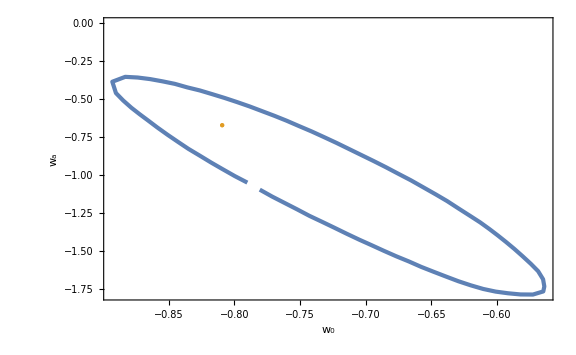

```mathematica
Show[ListPlot[DESY2ssorted,FrameLabel->{Subscript[w, 0],Subscript[w, a]}],ListPlot[{{wsol[t0],wasol[t0]}},PlotStyle->Directive[Color[2],PointSize[Large]],Joined->False]]
```

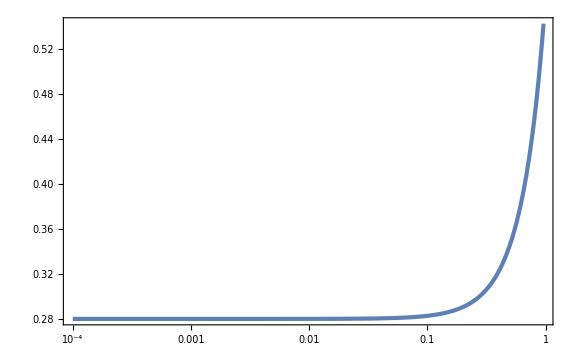

```mathematica
LogLinearPlot[xsol[t],{t,ti,t0},PlotRange->Full]
```

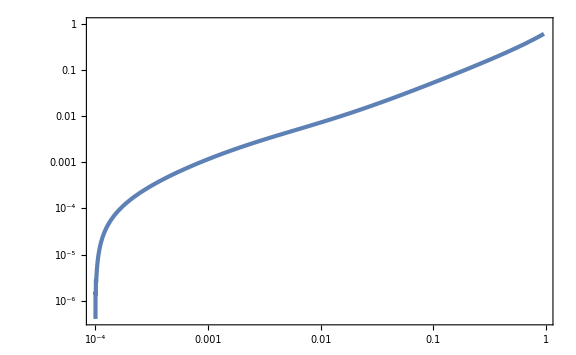

```mathematica
LogLogPlot[psol[t],{t,ti,t0}]
```

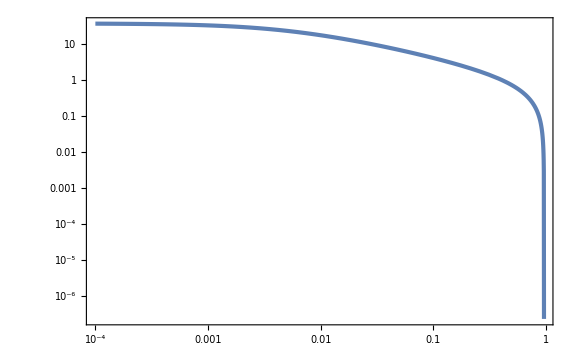

```mathematica
LogLogPlot[zsol[t],{t,ti,t0},PlotRange->Full]
```

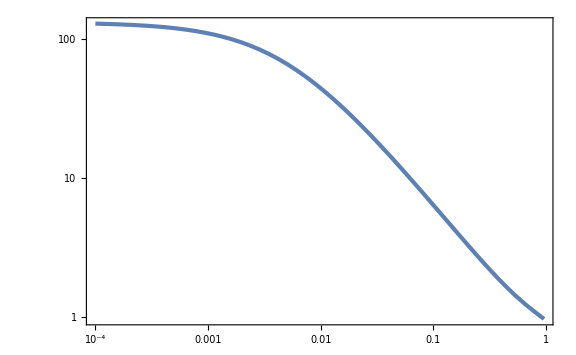

```mathematica
LogLogPlot[Hsol[t],{t,ti,t0}]
```

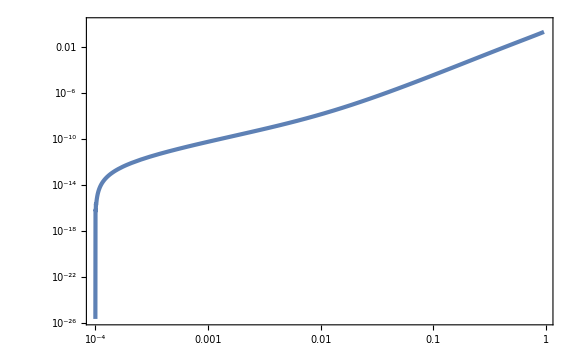

```mathematica
LogLogPlot[esol[t],{t,ti,t0}]
```

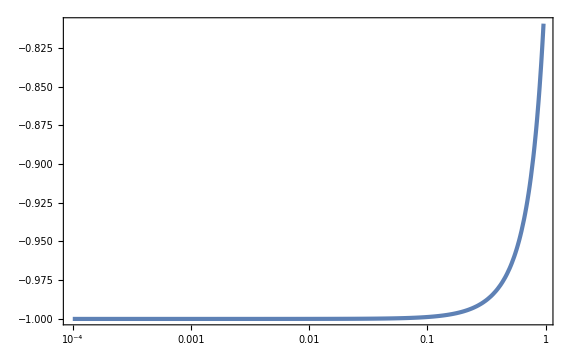

```mathematica
LogLinearPlot[wsol[t],{t,ti,t0},PlotRange->Full]
```

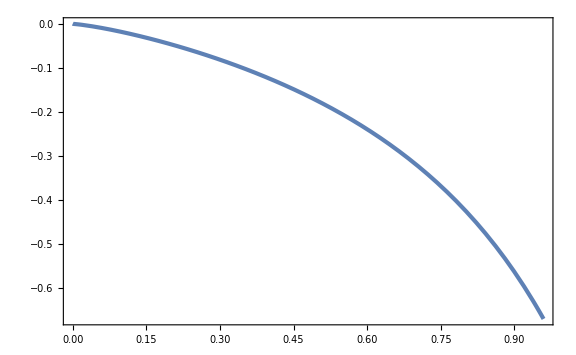

```mathematica
Plot[wasol[t],{t,ti,t0}]
```

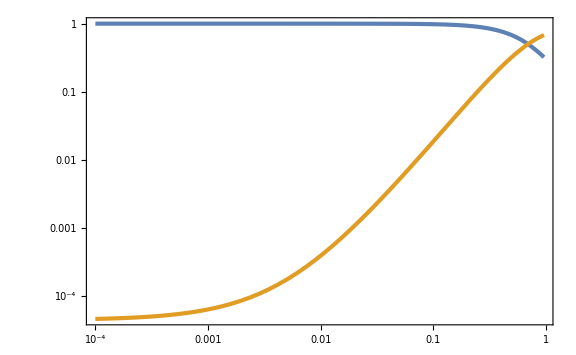

```mathematica
LogLogPlot[{(Ωm(1+zsol[t])^3)/(Ωm(1+zsol[t])^3+Ωs[xsol[t],psol[t]])/.{β->15/10,e10->4/10,Ωm->3/10},Ωs[xsol[t],psol[t]]/(Ωm(1+zsol[t])^3+Ωs[xsol[t],psol[t]])/.{β->15/10,e10->4/10,Ωm->3/10}},{t,ti,t0}]
```

### w/ DM

```mathematica
DESY2s=Import["DESY2s.csv"];
```

```mathematica
DESY2sMean=Mean[DESY2s]
```

{-0.723974,-1.06981}

```mathematica
DESY2spol=Sort[Table[{Norm[DESY2s[[i]]-DESY2sMean],ArcTan[(DESY2s[[i]]-DESY2sMean)[[1]],(DESY2s[[i]]-DESY2sMean)[[2]]]},{i,Length[DESY2s]}],#1[[2]]<#2[[2]]&];
```

```mathematica
DESY2ssorted=Table[{DESY2spol[[i,1]]Cos[DESY2spol[[i,2]]],DESY2spol[[i,1]]Sin[DESY2spol[[i,2]]]}+DESY2sMean,{i,Length[DESY2spol]}];
```

```mathematica
ListPlot[DESY2ssorted,FrameLabel->{Subscript[w, 0],Subscript[w, a]}]
```

-Graphics-

```mathematica
e10[w0_]=3/2(1+w0+R0)/(1+R0);
eϕ0[w0_]=3/2(1+w0)/(1+R0);
eM0[w0_]=3/2 R0/(1+R0);
```

```mathematica
eϕ0[w0]+eM0[w0]-e10[w0]//Simplify
```

0

```mathematica
-2/3(2eϕ0[w0](β+e10[w0])+(3w0)/(1+R0)eM0[w0])(1+R0)+(1-2/3 e10[w0])3w0 R0//Simplify
```

-((1+w0) (3+3 w0+2 β))

```mathematica
-2/3 e10[w0](2β+2e10[w0])/.{R0->0}
```

-((1+w0) (3 (1+w0)+2 β))

```mathematica
beta[w0_,wa_]=-wa/(2(1+w0))-3/2(1+w0);
```

```mathematica
-(1+w0)(3+3w0+2beta[w0,wa])//Simplify
```

wa

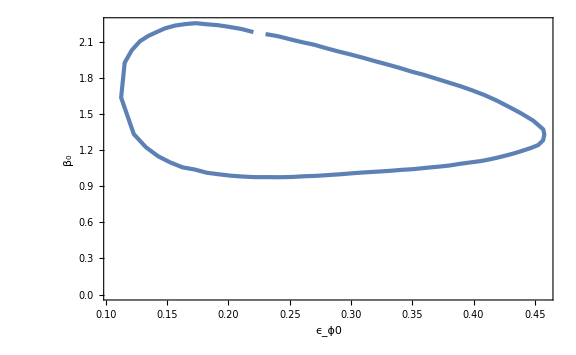

```mathematica
ListPlot[Map[{eϕ0[#[[1]]]/.{R0->3/7},beta[#[[1]],#[[2]]]/.{R0->3/7}}&,DESY2ssorted],FrameLabel->{Subscript[ϵ, ϕ0],Subscript[β, 0]}]
```